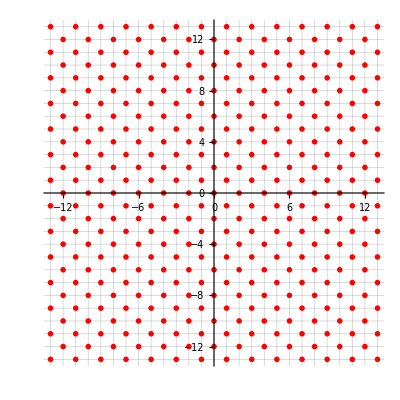

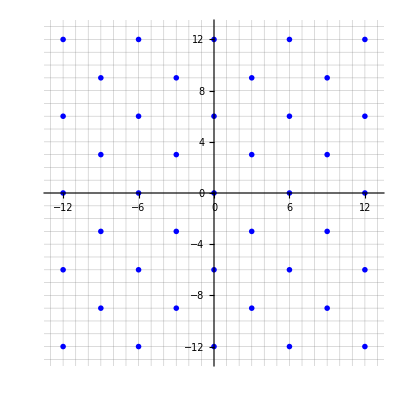

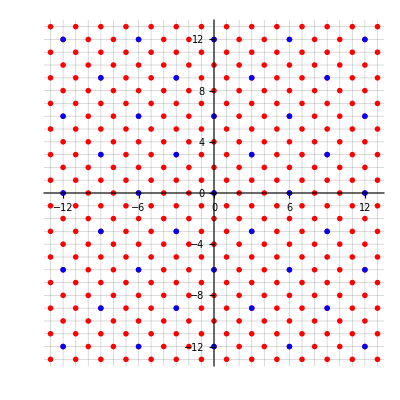

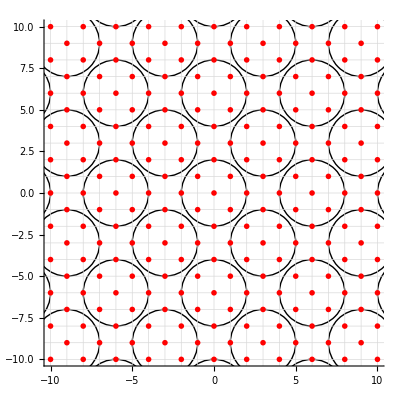

```mathematica
v1={1,1};
v2={1,-1};
varMax=20;
Reticulado=Select[Flatten[Table[i*v1+j*v2,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤14&];
DesenhoReticulado=ListPlot[Reticulado,AspectRatio->1,PlotStyle->{Red,PointSize[0.01]},GridLines->{Range[-14,14],Range[-14,14]},PlotRange->{{-13,13},{-13,13}}]


v3={0,6};
v4={3,3};
varMax=20;
Reticulado2=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤14&];
DesenhoReticulado2=ListPlot[Reticulado2,AspectRatio->1,PlotStyle->{Blue,PointSize[0.01]},GridLines->{Range[-14,14],Range[-14,14]},PlotRange->{{-13,13},{-13,13}}]

Show[DesenhoReticulado,DesenhoReticulado2]


BolaLee[r_,c_]:=Graphics[{Thickness[0.005],Opacity[0.2],FaceForm[Gray],EdgeForm[Directive[Gray]],Polygon[{c+{r,0},c+{0,r},c+{-r,0},c+{0,-r},c+{r,0}}]}];
BolasLee=Map[BolaLee[2,#]&,Reticulado2];
A=Show[BolasLee,DesenhoReticulado,Axes->True,GridLines->{Range[-10,10],Range[-10,10]},PlotRange->{{-10,10},{-10,10}}];


BolaEuclidiana[c_,r_]:=Graphics[Circle[c,r]];
BolasEuclidianas=Map[BolaEuclidiana[#,2]&,Reticulado2];

B=Show[BolasEuclidianas,DesenhoReticulado,Axes->True,GridLines->{Range[-10,10],Range[-10,10]},PlotRange->{{-10,10},{-10,10}}]
Show[A,DesenhoReticulado2]
```

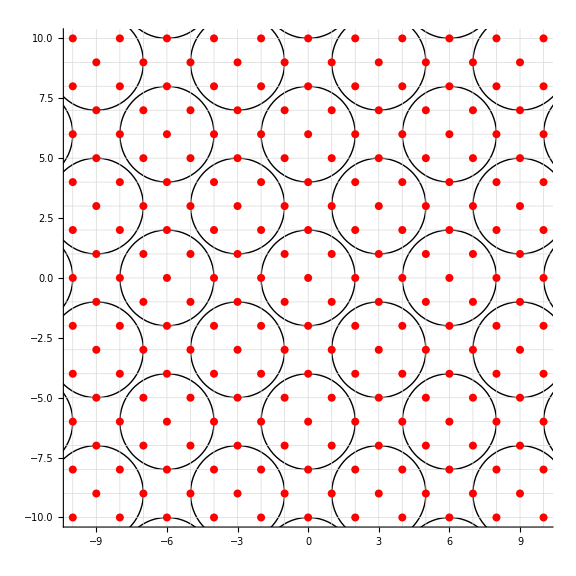

```mathematica
Show[B,ImageSize->Large]
```

```mathematica
Show[%567,Background->None]
```

-Graphics-

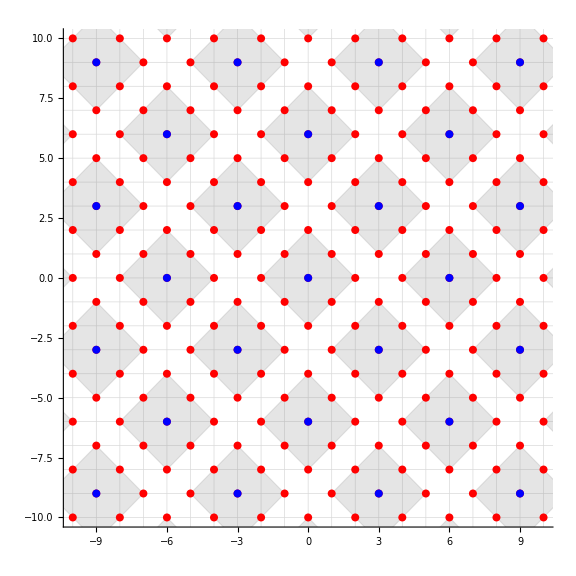

```mathematica
Show[%564,ImageSize->Large]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

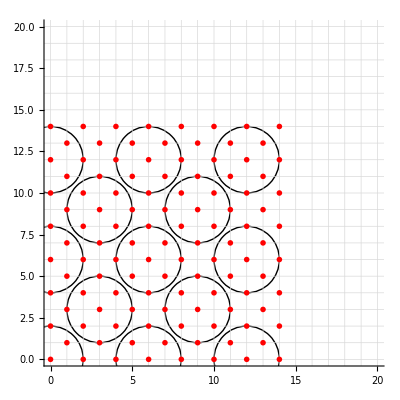

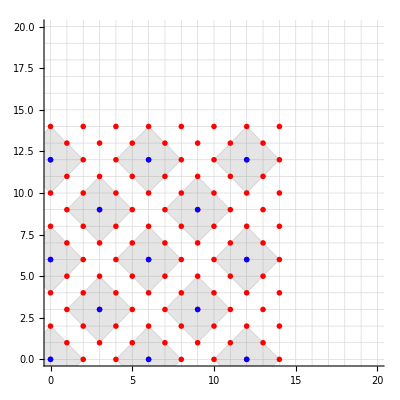

```mathematica
Show[%565,Background->None]
```